```mathematica
计算90°以内的周期与角振幅之间的关系
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than TraditionalForm`MachinePrecision digits of working precision to meet these tolerances.

T ≈ 0.0000471702 θ^2-2.81499×10^-6 θ+2.45818

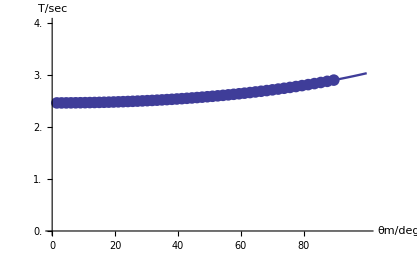

```mathematica
g=9.8;L=1.5;Ω=√(g/L);θT={};
Do[
ω0=v0/L;
s=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]],
θ[0]==0,θ'[0]==ω0},θ,{t,0,5}];
α=θ/.s[[1]];
θm1=FindMaximum[α[t],{t,0.5}];
θm2=FindMaximum[α[t],{t,3.3}];
T=(t/.θm2[[2]])-(t/.θm1[[2]]);
AppendTo[θT,{θm1[[1]]*180/π,T}],
{v0,0.1,5.4,0.1}]
g1=ListPlot[θT,AxesOrigin->{0,0},
PlotStyle->PointSize[0.02]];
θT=Fit[θT,{1,θ,θ^2,θ^3,θ^4,θ^5,θ^6},θ];
Print["T ≈ ",Take[θT,3]]
g2=Plot[θT,{θ,0,100},
PlotStyle->Thickness[0.004]];
Show[{g1,g2},AxesLabel->{"θm/deg","T/sec"},
PlotRange->{{0,100},{0,4}},
Ticks->{Range[0,90,10],Range[0,4,0.5]},
AxesStyle->Thickness[0.003]]
Clear[L,Ω,θT,ω0,s,T,θm1,θm2,g1,g2,α]
```